```mathematica
FindMaximum[{(81x+19)^1+(80(1-x)+20)^1,0≤x≤1},x]
```

{120.,{x→1.}}

```mathematica
FindMaximum[{(81x+19)^0.5+(80(1-x)+20)^0.5,0≤x≤1},x]
```

{15.4601,{x→0.512327}}

```mathematica
FindMaximum[{Log[81x+19]+Log[80(1-x)+20],0≤x≤1},x]
```

{8.18043,{x→0.507716}}

A cake with two regions has to be divided among 3 people with values: 
19 0 0 81
0 20 0 80.13
0 0 40 60

```mathematica
We can find an envy-.13-efficient division with this command:
```

```mathematica
Welfare[x_,y_,z_]:=Log[81x+19]+Log[80 y+20]+Log[60z+40]
```

```mathematica
FindMaximum[{Welfare[x,y,z],0<x<1, 0<y<1,0<z<1, x+y+z==1},{x,y,z}]
```

{11.8731,{x→0.48251,y→0.467078,z→0.0504124}}

```mathematica
Welfare2[x_,y_] := Welfare[x,y,1-x-y]
```

```mathematica
FindMaximum[{Welfare2[x,y],0<x<1,0<y<1,0<x+y<1},{{x,0},{y,0}}]
```

{11.8731,{x→0.48251,y→0.467078}}

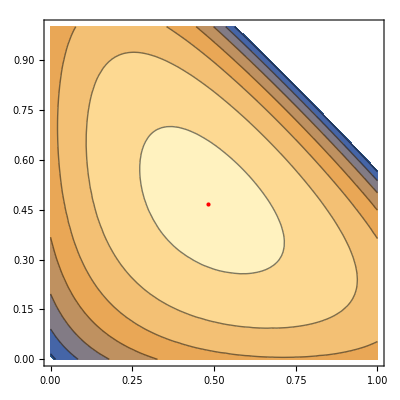

```mathematica
Show[ContourPlot[Welfare2[x,y],{x,0,1},{y,0,1}],Graphics[{Red,PointSize[Large],Point[{x,y}/.Last[%]]}]]
```

NMaximize calculates a global maximum. In this case it is identical to the local maximum of FindMaximum:

```mathematica
NMaximize[{Welfare2[x,y],0<x<1,0<y<1,0<x+y<1},{x,y}]
```

{11.8731,{x→0.48251,y→0.467078}}

```mathematica
Welfare3[x_,y_]:=(81x+19)+(80 y+20)+(60(1-x-y)+40)
```

```mathematica
NMaximize[{Welfare3[x,y],0<x<1,0<y<1,0<x+y<1},{x,y}]
```

{160.,{x→1.,y→0.}}

```mathematica
NMaximize[{Welfare3[x,y],{0≤x≤1,0≤y≤1,x+y≤1}},{x,y}, Integers]
```

{160.,{x→1,y→0}}